## Find the full formula directly from the graph using the additive procedure

```mathematica
SetsToSymbol2[s_, prefix_:"v"]:=Symbol[prefix<>StringRiffle[Map[StringJoin[Map[IntegerString[#,36]&,#]]&,s],"x"]]
```

```mathematica
FindFullFormula2[g_]:=Block[{formulaDepth=0},
Monitor[
formulaDepth=0;FindFullFormula2[g,Table[{v},{v,VertexList[g]}]],
formulaDepth
]
]
```

```mathematica
FindFullFormula2[g_,v_]:=Block[{edge,pos1,pos2,v2,result={}},
If[CompleteGraphQ[g],
result={SetsToSymbol2[Sort[Map[Sort[#]&,v],#1[[1]]<#2[[1]]&]]}
,
edge=First[EdgeList[GraphComplement[g]]];
Table[If[MemberQ[v[[k]],edge[[1]]],pos1=k],{k,Length[v]}];
Table[If[MemberQ[v[[k]],edge[[2]]],pos2=k],{k,Length[v]}];
v2=v;
v2[[pos1]]=Join[v2[[pos1]],v2[[pos2]]];
v2=Delete[v2,pos2];
result=Join[
FindFullFormula2[EdgeAdd[g,edge],v],
FindFullFormula2[VertexContract[g,{edge[[1]],edge[[2]]}],v2]
]
];
If[Length[result]>formulaDepth,formulaDepth=Length[result]];
result
]
```

```mathematica
FormulaGraphReverse4[formula_]:=Block[{sets=Map[SymbolToSets[#]&,ListofVars[formula]], edges={},vertices,vert={}},
Table[
Table[
If[IsRefinement[s1,s2]&&(Length[s1]==Length[s2]-1), AppendTo[edges,SetsToSymbol[s1]->SetsToSymbol[s2]]]
,{s2,Select[sets,#≠s1&]}
]
,{s1,sets}];
vert = Table[SetsToSymbol[s],{s,sets}];
vertices = Table[SetsToSymbol[s]-> Framed[Rotate[Length[s],Pi/6],Background->LightYellow],{s,sets}];
Graph[vert,edges,VertexLabels->vertices, GraphLayout->"LayeredDigraphEmbedding"]
]
```

```mathematica
Map[Factor[ChromaticPolynomial[CompleteGraph[Length[SymbolToSets[#]]],x]]&,FindFullFormula2[ReadGrof[5]]]//Total//Factor
```

(-3+x)^4 (-2+x) (-1+x) x

```mathematica
ChromaticPolynomial[ReadGrof[5],x]//Factor
```

(-3+x)^4 (-2+x) (-1+x) x

```mathematica
MatrixForm[Map[PadRight[#,10]&,Table[StirlingS2[n,k],{n,1,10},{k,n}]],TableHeadings->{Range[10],Range[10]}]
```

( | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3 | 1 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 1 | 7 | 6 | 1 | 0 | 0 | 0 | 0 | 0 | 0
5 | 1 | 15 | 25 | 10 | 1 | 0 | 0 | 0 | 0 | 0
6 | 1 | 31 | 90 | 65 | 15 | 1 | 0 | 0 | 0 | 0
7 | 1 | 63 | 301 | 350 | 140 | 21 | 1 | 0 | 0 | 0
8 | 1 | 127 | 966 | 1701 | 1050 | 266 | 28 | 1 | 0 | 0
9 | 1 | 255 | 3025 | 7770 | 6951 | 2646 | 462 | 36 | 1 | 0
10 | 1 | 511 | 9330 | 34105 | 42525 | 22827 | 5880 | 750 | 45 | 1)

```mathematica
ChromaticPolynomial[ReadGrof[6],x]//Factor
```

(-3+x) (-2+x) (-1+x) x (-32+29 x-9 x^2+x^3)

```mathematica
CompleteBaseCoeff[ChromaticPolynomial[ReadGrof[6],x]]
```

{0,0,0,0,4,9,6,1}

```mathematica
MatrixForm[Map[PadLeft[#,10]&,Table[CompleteBaseCoeff[ChromaticPolynomial[ReadGrof[k],x]],{k,2,30}]],TableHeadings->{Range[30],Range[10]}]
```

( | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 3 | 1
3 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 3 | 3 | 1
4 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 7 | 6 | 1
5 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 9 | 6 | 1
6 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 10 | 6 | 1
7 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 7 | 6 | 1
8 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 7 | 6 | 1
9 | 0 | 0 | 0 | 0 | 0 | 1 | 15 | 25 | 10 | 1
10 | 0 | 0 | 0 | 0 | 0 | 5 | 25 | 28 | 10 | 1
11 | 0 | 0 | 0 | 0 | 0 | 1 | 15 | 25 | 10 | 1
12 | 0 | 0 | 0 | 0 | 0 | 1 | 15 | 25 | 10 | 1
13 | 0 | 0 | 0 | 0 | 0 | 4 | 22 | 27 | 10 | 1
14 | 0 | 0 | 0 | 0 | 0 | 4 | 22 | 27 | 10 | 1
15 | 0 | 0 | 0 | 0 | 0 | 1 | 15 | 25 | 10 | 1
16 | 0 | 0 | 0 | 0 | 0 | 1 | 15 | 25 | 10 | 1
17 | 0 | 0 | 0 | 0 | 0 | 3 | 26 | 29 | 10 | 1
18 | 0 | 0 | 0 | 0 | 0 | 4 | 22 | 27 | 10 | 1
19 | 0 | 0 | 0 | 0 | 0 | 4 | 22 | 27 | 10 | 1
20 | 0 | 0 | 0 | 0 | 1 | 11 | 30 | 29 | 10 | 1
21 | 0 | 0 | 0 | 0 | 0 | 1 | 15 | 25 | 10 | 1
22 | 0 | 0 | 0 | 0 | 0 | 1 | 15 | 25 | 10 | 1
23 | 0 | 0 | 0 | 0 | 1 | 31 | 90 | 65 | 15 | 1
24 | 0 | 0 | 0 | 0 | 4 | 48 | 103 | 67 | 15 | 1
25 | 0 | 0 | 0 | 0 | 5 | 55 | 109 | 68 | 15 | 1
26 | 0 | 0 | 0 | 0 | 1 | 31 | 90 | 65 | 15 | 1
27 | 0 | 0 | 0 | 0 | 1 | 31 | 90 | 65 | 15 | 1
28 | 0 | 0 | 0 | 0 | 1 | 31 | 90 | 65 | 15 | 1
29 | 0 | 0 | 0 | 0 | 4 | 48 | 103 | 67 | 15 | 1)

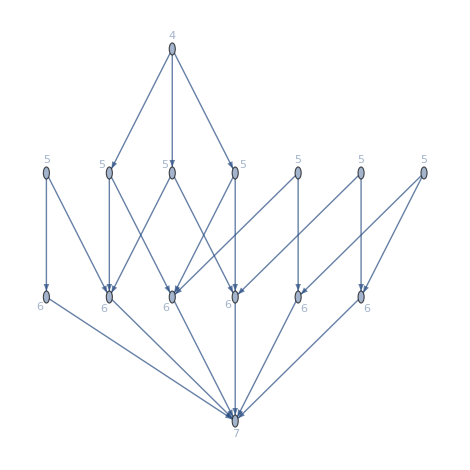

```mathematica
FormulaGraphReverse4[FindFullFormula2[ReadGrof[5]]]
```